```mathematica
Quit[];
```

Set::wrsym: Symbol ⅈ is Protected.

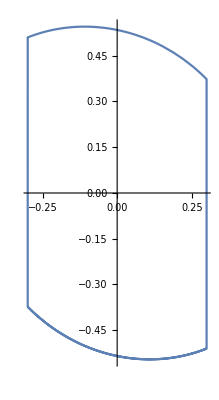

```mathematica
(* Equation of motion of pendulum *)
(* θ = angle of the pendulum as measured ccw from vertical*)
(* ζ = damping ratio *)
(* u = externally applied torque *)

EoM={θ''[t] + 2 ζ θ'[t] + θ[t]  == 0};

(* Configuration at beginning of motion *)
InitCon = {θ[0] == α, θ'[0]==-Ω};

(* Prior to Impulse at time τ *)
FinCon = {θ[τ] == -α, θ'[τ]==-Ω η};

(* Parameters: *)
U = 2 α / τ; U = 0.5; amplitued = π/4 ; α = 0.3; ζ = 0.1; τ = 1.2; Ω = 0.510; η = 0.731;  k = 1;

(* Using initial conditions *)
sol = NDSolve[Join[EoM, InitCon], {θ, θ'}, {t, 0, τ}];

(* Using final conditions *)
sol2 = NDSolve[Join[EoM, FinCon], {θ, θ'}, {t, 0, τ}];


(* Impulse ?????? *)
EoMI={θ''[t] + 2 ζ θ'[t] + θ[t]  == I};
(* Control Law *)
I = Piecewise[{{Ω*(1+η), t== (2*k-1)*τ}, {-Ω*(1+η), t== 2*k*τ}}];
sol3 = NDSolve[Join[EoMI, FinCon ], {θ, θ'}, {t, τ, 2*τ}];


(* At time `τ impulse is applied *)
(*I = ∫_τmin^τplus u[t]ⅆt*)


(* After Impulse at time τ *)
InitConAfter = {θ[τ] == -α, θ'[τ] == Ω};
sol4 = NDSolve[Join[EoM, InitConAfter ], {θ, θ'}, {t, τ, 2*τ}];

(* Configuration at beginning of motion *)
InitCon = {θ[2τ] == α, θ'[2τ]==-Ω};
(* Returnign to original *)
sol5 = NDSolve[Join[EoM, InitCon], {θ, θ'}, {t, 2 τ, 3τ}];

(*ParametricPlot[{θ[t]/.sol[[1]] /.t-> T, θ'[t]/.sol[[1]] /.t-> T}, {T, 0, 1.2}]
ParametricPlot[{θ[t]/.sol2[[1]] /.t-> T, θ'[t]/.sol2[[1]] /.t-> T}, {T, 0, 1.2}]
ParametricPlot[{θ[t]/.sol3[[1]] /.t-> T, θ'[t]/.sol3[[1]] /.t-> T}, {T, τ, 2 τ}]
ParametricPlot[{θ[t]/.sol4[[1]] /.t-> T, θ'[t]/.sol4[[1]] /.t-> T}, {T, τ, 2 τ}]*)

limitCycleθ = Piecewise[{{θ[t]/.sol2[[1]] /.t-> T, 0≤ T≤ τ},{θ[t]/.sol4[[1]] /.t-> T,τ≤T≤2 τ}, {θ[t]/.sol5[[1]] /.t-> T, 2 τ≤ T≤ 3 τ}}];
limitCycleθdot = Piecewise[{{θ'[t]/.sol2[[1]] /.t-> T, 0≤ T≤ τ},{θ'[t]/.sol4[[1]] /.t-> T ,τ≤ T≤2 τ}, {θ'[t]/.sol5[[1]] /.t-> T, 2 τ≤ T≤ 3τ}}];
ParametricPlot[{limitCycleθ, limitCycleθdot}, {T, 0, 3τ}]
```